# Trabalho em Grupo ( Opcional ) - Campo Elétrico

## Fundamentos de Física 3

Aluno 1: Pedro Henrique Passos Rocha 
Aluno 2: Catterina Vittorazzi Salvador
Aluno 3: João Pedro Teixeira Pontual

1. Use o software Wolfram Mathematica para calcular a integral que resulta na expressão do campo
elétrico E⃗ (ρ, θ, z), para uma linha de cargas infinita, com densidade linear constante λ_0 é :

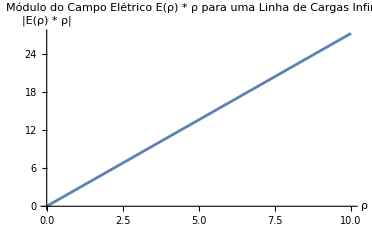
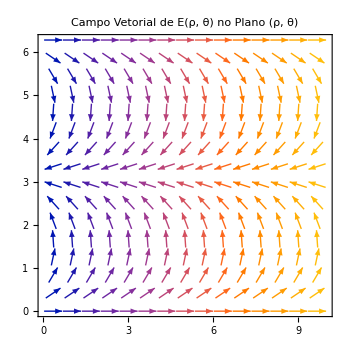
```mathematica
(*Faça o gráfico do módulo do campo elétrico E(ρ)×ρ*)Plot[Abs[E ρ],{ρ,0.01,10},AxesLabel->{"ρ","|E(ρ) * ρ|"},PlotLabel->"Módulo do Campo Elétrico E(ρ) * ρ para uma Linha de Cargas Infinita",PlotRange->All]

-Graphics-
(*Defina as componentes do campo elétrico em coordenadas polares*)Ex[ρ_,θ_]=E ρ Cos[θ];
Ey[ρ_,θ_]=E ρ Sin[θ];

(*Faça o gráfico do campo vetorial no plano (ρ,θ)*)
VectorPlot[{Ex[ρ,θ],Ey[ρ,θ]},{ρ,0.01,10},{θ,0,2 π},VectorScale->Small,VectorStyle->Arrowheads[0.015],PlotLabel->"Campo Vetorial de E(ρ, θ) no Plano (ρ, θ)"]

-Graphics-
(*Defina a componente z do campo elétrico*)Ez[ρ_,θ_,z_]=0; (*Para uma linha de carga infinita,o campo elétrico não depende de z*)

(*Faça o gráfico do campo vetorial no espaço 3D*)
VectorPlot3D[{Ex[ρ,θ],Ey[ρ,θ],Ez[ρ,θ,z]},{ρ,0.01,10},{θ,0,2 π},{z,-10,10},VectorScale->Small,VectorStyle->Arrowheads[0.015],PlotLabel->"Campo Vetorial de E(ρ, θ, z) no Espaço 3D"]

-Graphics3D-
```

2. Use o software Wolfram Mathematica para calcular a integral na expressão do campo elétrico E⃗, sobre um ponto z arbitrário do eixo do anel carregado (usualmente eixo z) com uma densidade de cargas linear constante : 
	E (z) =  1/(4 π ε0)×Qz/((z^2+R^2)^(3/2))
Onde Q é carga elétrica total do anel e R é o raio do anel . Use o software Wolfram Mathematica para fazer gráfico de : 
a) E (z)*z;
b) E (z, R)*(z, R) 
Dica : considere no gráfico (4 π ε0) igual a 1, além de Q também igual a 1 (e R igual a 1 na letra (a)) .

-Q/(4 π √(R^2+z^2) ε0)

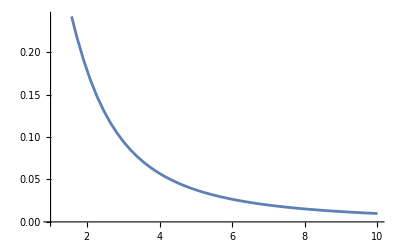

-Graphics3D-

```mathematica
Integrate[1/(4π*ε0)×(Q*z)/((z^2+R^2)^(3/2)),z]
Plot[z/((z^2+1)^(3/2)),{z,1,10}]
Plot3D[z/((z^2+R^2)^(3/2)),{z,1,10},{R,1,10}]
```